# Comparison between the triangle plaquette model and the triangle continuum model.

# Triangular Plaquette Model H = (2/g^2) E^2 + 2/g^2 B^2 ---> (2/g^2)(E1^2 +E2^2 + E3^2) + (1/g^2) (1 - Cos[theta1, +theta2 + theta3)) With commutators [E_i, e^{itheta_j}] = delta_[ij} e^{itheta_j}

```mathematica
(* All terms are positve: With Wilson Plaq
B^2(s) = (1/2)Tr[2 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:    U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)
```

```mathematica
(*Sigma operators*)
```

```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
SigmaP= (Sigma[1]+ I*Sigma[2])/2;
SigmaM= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
NQubits = 9
```

9

```mathematica
(*  zero point terms ((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit]*)
```

## Plaquette term

```mathematica
(*Single plaquette term at s-th layer *)
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

{6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

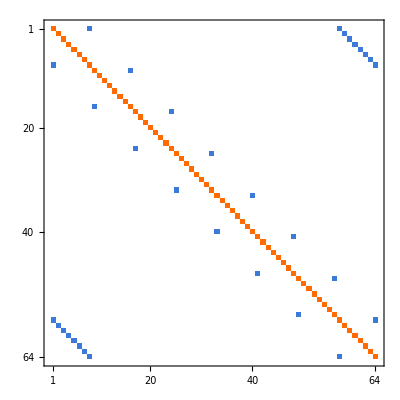

```mathematica
Bsingle[s_, nQubit_] :=KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]];
(*Sum over all layers*)
B[nQubit_] := - Sum[Bsingle[s, nQubit],{s,1,nQubit/3}]  + (nQubit/3)  IdentityMatrix[2^nQubit]
Eigenvalues[B[6]]
Eigenvalues[B[9]]
MatrixPlot[B[6]]
```

## Electric links between neighborhood layers sigmaz_{j + 3} x sigmaz_j note + convention on Qubit operators

```mathematica
Es[nQubit_] :=   Sum[FullSigma[3,Mod[j+3,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] +  (nQubit - 6 Mod[nQubit,2])*IdentityMatrix[2^nQubit]
Eigenvalues[Es[6]]
```

{12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0}

## XX + YY chain

Eigenvalues[SparseArrayXY[6]]

Eigenvalues[SparseArrayXY[9]]

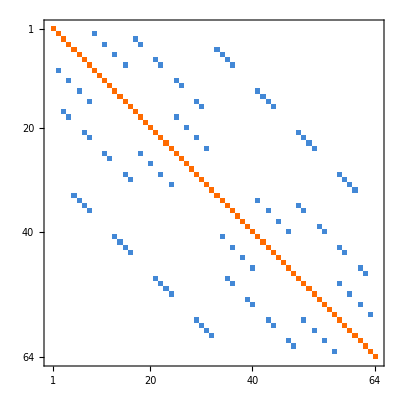

```mathematica
XY[nQubit_] :=- Sum[FullSigma[1,Mod[j+3,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
- Sum[FullSigma[2,Mod[j+3,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]  + 2 nQubit * IdentityMatrix[2^nQubit] 
Eigenvalues[SparseArrayXY[6]]
Eigenvalues[SparseArrayXY[9]]
MatrixPlot[XY[6]]
```

## Define Hamiltonian

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
(* H0[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]
H1[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]+
((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit] *)
```

```mathematica
H[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*Es[nQubit] + (1/(2*g^2))* B[nQubit]]+  (alpha/(2*g^2))*XY[nQubit]
```

```mathematica
Eigenvalues[Es[6]]
```

{12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[B[6]]
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

```mathematica
Eigenvalues[XY[6]]
```

{24,20,20,20,20,20,20,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,0}

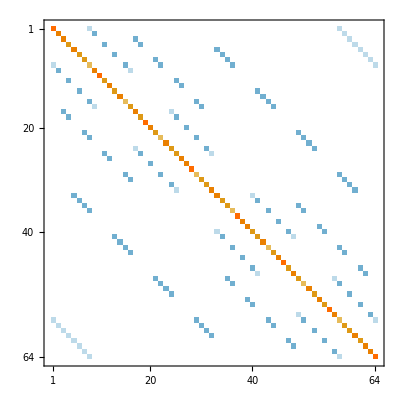

```mathematica
MatrixPlot[H[1, 1, 6]]
```

## Eigenvalue spectrum of H(g, alpha)

```mathematica
Eigs[g_, alpha_, nQubit_, k_] := Sort[Eigenvalues[H[g, alpha, nQubit], k], Less]
```

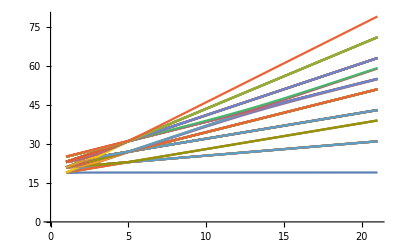

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

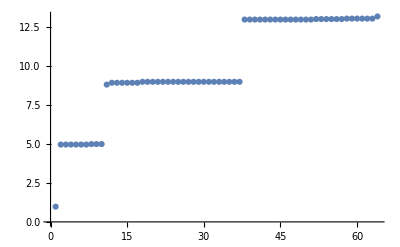

```mathematica
ListPlot[Eigs[1, 1,6 , 2^6]]
```

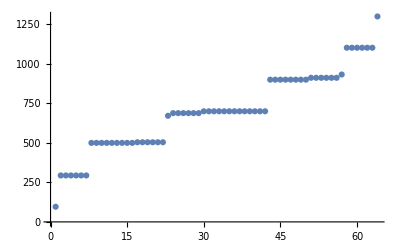

```mathematica
ListPlot[Eigs[0.1, 1,6 , 2^6]]
```

# Gauge Rotation Operators

```mathematica
(* Gauge Rotation Operators J12, J23, J31 *)
J12[nQubit_] := Sum[FullSigma[3,Mod[s*3+1,nQubit], nQubit]-FullSigma[3, Mod[s*3+2,nQubit], nQubit],{s,0,nQubit/3-1}]
J23[nQubit_] := Sum[FullSigma[3,Mod[s*3+2,nQubit], nQubit]-FullSigma[3, Mod[s*3+3,nQubit], nQubit],{s,0,nQubit/3-1}]
J31[nQubit_] := Sum[FullSigma[3,Mod[s*3+3,nQubit], nQubit]-FullSigma[3, Mod[s*3+1,nQubit], nQubit],{s,0,nQubit/3-1}]
```

## Eigenvalues (Diagonal Elements) of Gauge Rotation Operators

```mathematica
D12 = Normal[Diagonal[J12[NQubits]]]
```

{0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,-4,-4,-6,-6,-2,-2,-4,-4,-4,-4,-6,-6,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,-4,-4,-6,-6,-2,-2,-4,-4,-4,-4,-6,-6,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,4,4,2,2,6,6,4,4,4,4,2,2,6,6,4,4,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,4,4,2,2,6,6,4,4,4,4,2,2,6,6,4,4,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0,-2,-2,-4,-4,0,0,-2,-2,-2,-2,-4,-4,0,0,-2,-2,2,2,0,0,4,4,2,2,2,2,0,0,4,4,2,2,0,0,-2,-2,2,2,0,0,0,0,-2,-2,2,2,0,0}

```mathematica
D23 = Normal[Diagonal[J23[NQubits]]]
```

{0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,4,6,4,6,2,4,2,4,2,4,2,4,0,2,0,2,4,6,4,6,2,4,2,4,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,4,6,4,6,2,4,2,4,2,4,2,4,0,2,0,2,4,6,4,6,2,4,2,4,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,-6,-4,-6,-4,-2,0,-2,0,-4,-2,-4,-2,-4,-2,-4,-2,-6,-4,-6,-4,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,-6,-4,-6,-4,-2,0,-2,0,-4,-2,-4,-2,-4,-2,-4,-2,-6,-4,-6,-4,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,0,2,0,2,-2,0,-2,0,2,4,2,4,0,2,0,2,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0,-2,0,-2,0,-4,-2,-4,-2,0,2,0,2,-2,0,-2,0}

```mathematica
D31 = Normal[Diagonal[J31[NQubits]]]
```

{0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,-4,-6,-2,-4,-4,-6,-2,-4,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,-2,-4,0,-2,-2,-4,0,-2,-4,-6,-2,-4,-4,-6,-2,-4,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,4,2,6,4,4,2,6,4,2,0,4,2,2,0,4,2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,4,2,6,4,4,2,6,4,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,-4,-6,-2,-4,-4,-6,-2,-4,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,-2,-4,0,-2,-2,-4,0,-2,-4,-6,-2,-4,-4,-6,-2,-4,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,4,2,6,4,4,2,6,4,2,0,4,2,2,0,4,2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,4,2,6,4,4,2,6,4,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0,0,-2,2,0,0,-2,2,0,-2,-4,0,-2,-2,-4,0,-2,2,0,4,2,2,0,4,2,0,-2,2,0,0,-2,2,0}

```mathematica
(*Check if they sum up to zero *)
```

```mathematica
D12 + D23 + D31
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Sort[D12^2+  D23 ^2 + D31^2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,72,72,72,72,72,72}

## Permutation Rule Ordered by Square Sum Eigenvalues

```mathematica
perm = Ordering[D12^2+ D23^2+D31^2]
```

{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,225,232,239,246,253,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,477,484,491,498,505,512,2,3,4,5,6,7,9,11,13,16,17,18,21,24,25,30,31,32,33,34,35,40,41,44,47,48,49,52,54,56,58,59,60,61,62,63,65,67,69,72,79,81,86,87,88,93,95,97,100,103,104,107,111,114,115,116,117,118,119,121,123,125,128,129,130,133,136,137,142,143,144,150,157,158,161,164,166,168,170,171,172,173,174,175,178,182,185,186,189,192,193,198,199,200,205,207,213,214,221,226,227,228,229,230,231,233,235,237,240,241,242,245,248,249,254,255,256,257,258,259,264,265,268,271,272,273,276,278,280,282,283,284,285,286,287,292,299,300,306,308,313,314,315,320,321,324,327,328,331,335,338,339,340,341,342,343,345,347,349,352,355,356,363,369,370,371,376,377,380,383,384,385,388,390,392,394,395,396,397,398,399,402,406,409,410,413,416,418,420,425,426,427,432,434,441,444,446,448,450,451,452,453,454,455,457,459,461,464,465,466,469,472,473,478,479,480,481,482,483,488,489,492,495,496,497,500,502,504,506,507,508,509,510,511,12,14,20,23,26,27,38,39,42,45,51,53,68,70,75,77,82,83,89,96,98,101,105,112,124,126,132,135,138,139,146,149,153,160,163,165,177,184,188,191,194,195,201,208,209,216,222,223,236,238,244,247,250,251,262,263,266,269,275,277,290,291,297,304,305,312,318,319,322,325,329,336,348,350,353,360,364,367,374,375,378,381,387,389,401,408,412,415,417,424,430,431,436,438,443,445,460,462,468,471,474,475,486,487,490,493,499,501,10,19,28,37,46,55,66,73,80,84,91,94,102,108,109,122,131,140,145,152,154,159,167,180,181,187,196,203,206,210,215,217,224,234,243,252,261,270,279,289,296,298,303,307,310,317,326,332,333,346,354,359,361,368,373,382,391,404,405,411,419,422,429,433,440,447,458,467,476,485,494,503,76,78,90,92,106,110,148,151,155,156,179,183,202,204,211,212,218,219,294,295,301,302,309,311,330,334,357,358,362,365,403,407,421,423,435,437,74,147,220,293,366,439}

```mathematica
(* Count the number of zeros *)
```

```mathematica
NZero = Count[D12^2+ D23^2+D31^2, 0]
```

56

## The Permutated Hamiltonian Looks It Consists of Block Sectors with Sub-square Matrices

```mathematica
PermHamiltonian[g_, alpha_, nQubits_] := H[g, alpha, nQubits][[perm, perm]]
```

```mathematica
MatrixPlot[PermHamiltonian[1, 1, NQubits]]
```

-Graphics-

## The sub matrix with basis corresponding to zero eigenvalues

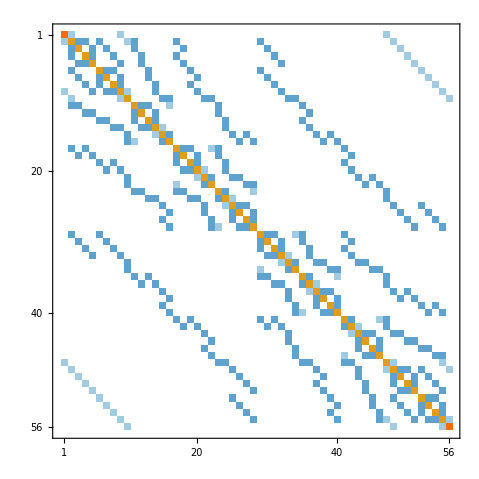

```mathematica
ZeroHamiltonian[g_, alpha_, nQubits_]  := PermHamiltonian[g, alpha, nQubits][[1;;NZero, 1;;NZero]]
ZeroH = ZeroHamiltonian[1, 1, NQubits];
MatrixPlot[ZeroH]
```

## Eigenvalue Spectrum of the Sub-Hamiltonian

```mathematica
Eigenvalues[ZeroH]//N
```

{16.6751,16.6184,14.,14.,14.,13.8536,13.7066,13.7066,13.7066,13.7066,13.376,13.376,13.376,13.376,13.1269,13.,13.,13.,11.0457,11.,11.,11.,11.,10.6398,10.6398,10.6398,10.6398,10.5811,10.5811,10.5811,10.5811,10.5,10.5,10.3055,10.3055,10.3055,10.3055,10.,10.,10.,10.,9.72056,7.81847,7.81847,7.81847,7.81847,7.41886,7.41886,7.41886,7.41886,7.15362,7.15362,7.15362,7.15362,4.92559,4.03415}

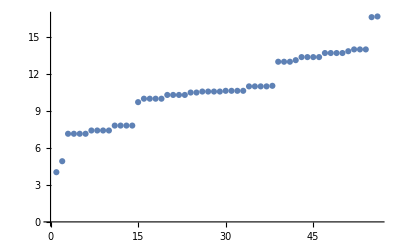

```mathematica
ListPlot[Sort[N[Eigenvalues[Normal[ZeroH]]]]]
```

## What if we change the value of g?

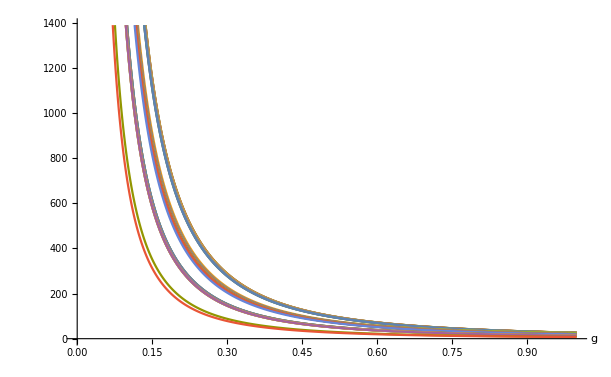

```mathematica
ListPlot[Transpose[Table[Eigenvalues[ZeroHamiltonian[g, 2, NQubits]], {g, 0.01, 1, 0.001}]], Joined->True, DataRange->{0.01, 1}, AxesLabel-> {"g", ""}]
```

```mathematica
EigenSpectra:= Sort[Eigenvalues[ZeroHamiltonian[0.1, 1.0, NQubits]]]
EigenSpectra//N
lambda0= EigenSpectra [[1]]//N
lambda1 = EigenSpectra [[2]]//N
(1/(lambda1 - lambda0))( EigenSpectra+ lambda1 - 2 lambda0)//N
```

{402.643,491.908,715.362,715.362,715.362,715.362,741.886,741.886,741.886,741.886,781.847,781.847,781.847,781.847,933.313,1000.,1000.,1000.,1000.,1004.89,1030.55,1030.55,1030.55,1030.55,1050.,1050.,1058.11,1058.11,1058.11,1058.11,1063.98,1063.98,1063.98,1063.98,1094.17,1100.,1100.,1100.,1100.,1151.58,1300.,1300.,1300.,1319.93,1337.6,1337.6,1337.6,1337.6,1370.66,1370.66,1370.66,1370.66,1400.,1400.,1400.,1401.68}

402.643

491.908

{1.,2.,4.50325,4.50325,4.50325,4.50325,4.80039,4.80039,4.80039,4.80039,5.24805,5.24805,5.24805,5.24805,6.94486,7.69192,7.69192,7.69192,7.69192,7.74673,8.03416,8.03416,8.03416,8.03416,8.25205,8.25205,8.34295,8.34295,8.34295,8.34295,8.40865,8.40865,8.40865,8.40865,8.74692,8.81218,8.81218,8.81218,8.81218,9.38995,11.0527,11.0527,11.0527,11.2759,11.4739,11.4739,11.4739,11.4739,11.8442,11.8442,11.8442,11.8442,12.1729,12.1729,12.1729,12.1918}

# Continuum Model Change varables preserving the computors (and redefing charge!) H = (2/g^2)p^2 + (1/g^2) (1 - Cos[theta]) + p12^2 +p23^2 + p31^2 with theta = theta1, +theta2 + theta3 and p = (E1 +E2 + E3)/ 3 External flux/gauge opeartors pij = E_i - E_j

```mathematica
Dia[n_]:= Table[i^2,{i,-n,n}]
Dia[5]
```

{25,16,9,4,1,0,1,4,9,16,25}

# This initializs the matrix for one plaquette, where a is the strength of the magnetic part relative to electric part.

```mathematica
Mat[n_,g_]:=
Table[ (g^2/2)KroneckerDelta[i,j] i^2+ (1/g^2)( 2 KroneckerDelta[i,j] -  KroneckerDelta[i,j+1]-KroneckerDelta[i,j-1]),{i,-n,n},{j,-n,n}]
MatrixForm[Mat[4,g]]
```

(2/g^2+8 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/g^2 | 2/g^2 | -1/g^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+8 g^2)

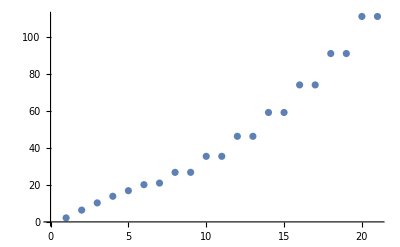

```mathematica
ListPlot[Sort[Re[Eigenvalues[(2/0.795^2)Mat[10,0.795]]],Less]]
```

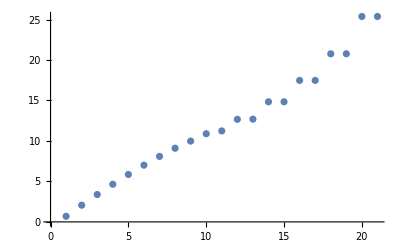

```mathematica
ListPlot[Sort[Re[Eigenvalues[Mat[10,0.6]]],Less]]
```

```mathematica
Dat=Table[Sort[Re[Eigenvalues[Mat[18,g], Method->"Banded"]],Less],{g,0.1,2.1,0.05}];
```

```mathematica
Here one can see how the level degenracy is split as we increase the magnetic term
as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]
```

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]

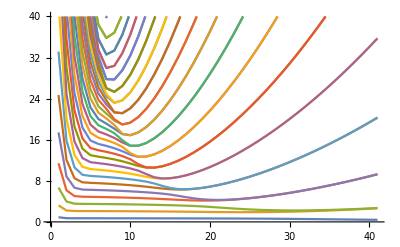

```mathematica
ListPlot[Transpose[Dat], Joined->True,PlotRange->{0,40}]
```

```mathematica
Length[Dat]
```

41

```mathematica
Here is the result with plaquette = 0 and with plaquette = 20, showing that the low energy degrees of freedom have a linear spectrum once magnetic term is strong
```

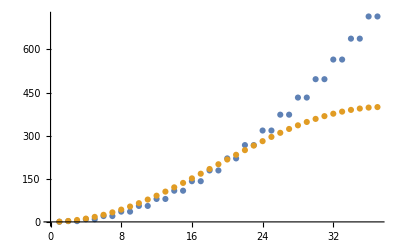

```mathematica
ListPlot[{Dat[[41]],Dat[[1]]}]
```

```mathematica
ListPlot[{Dat[[1]], Sort[Eigenvalues[ZeroHamiltonian[0.1, 1, 6]]]}]
```

Part::partw: Part 71 of {{700.06, 0., 0., 0., 0., 0., 0., -50., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 14 »}, « 49 », « 14 »} does not exist.

Part::take: Cannot take positions 1 through 56 in {{700.06, 0., 0., 0., 0., 0., 0., -50., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 14 »}, « 49 », « 14 »} ⟦ {1, 8, 15, 22, 29, 36, 43, 50, 57, « 33 », 400, 414, 428, 442, 449, 456, 463, 470, « 462 »}, « 1 » ⟧.

ListPlot::lpn: {{0.905888, 3.2249, 6.68274, 11.4186, 17.4351, 24.6989, 33.1625, 42.7691, « 21 », 358.423, 368.026, 376.484, 383.739, 389.739, 394.437, 397.796, 399.568}, « 1 »} is not a list of numbers or pairs of numbers.

ListPlot[{{0.905888,3.2249,6.68274,11.4186,17.4351,24.6989,33.1625,42.7691,53.4533,65.1424,77.7566,91.2098,105.41,120.261,135.66,151.503,167.681,184.084,200.6,217.116,233.519,249.697,265.539,280.938,295.788,309.988,323.44,336.053,347.741,358.423,368.026,376.484,383.739,389.739,394.437,397.796,399.568},Eigenvalues[{{700.06,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.},{0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.},{0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.},{0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.},{0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.},{0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.},{0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.},{-50.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.},{0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.},{0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.},{-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-50.},{0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.},{0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.},{0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.},{0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.},{0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.},{0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.},{0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.06}}⟦{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,225,232,239,246,253,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,477,484,491,498,505,512,2,3,4,5,6,7,9,11,13,16,17,18,21,24,25,30,31,32,33,34,35,40,41,44,47,48,49,52,54,56,58,59,60,61,62,63,65,67,69,72,79,81,86,87,88,93,95,97,100,103,104,107,111,114,115,116,117,118,119,121,123,125,128,129,130,133,136,137,142,143,144,150,157,158,161,164,166,168,170,171,172,173,174,175,178,182,185,186,189,192,193,198,199,200,205,207,213,214,221,226,227,228,229,230,231,233,235,237,240,241,242,245,248,249,254,255,256,257,258,259,264,265,268,271,272,273,276,278,280,282,283,284,285,286,287,292,299,300,306,308,313,314,315,320,321,324,327,328,331,335,338,339,340,341,342,343,345,347,349,352,355,356,363,369,370,371,376,377,380,383,384,385,388,390,392,394,395,396,397,398,399,402,406,409,410,413,416,418,420,425,426,427,432,434,441,444,446,448,450,451,452,453,454,455,457,459,461,464,465,466,469,472,473,478,479,480,481,482,483,488,489,492,495,496,497,500,502,504,506,507,508,509,510,511,12,14,20,23,26,27,38,39,42,45,51,53,68,70,75,77,82,83,89,96,98,101,105,112,124,126,132,135,138,139,146,149,153,160,163,165,177,184,188,191,194,195,201,208,209,216,222,223,236,238,244,247,250,251,262,263,266,269,275,277,290,291,297,304,305,312,318,319,322,325,329,336,348,350,353,360,364,367,374,375,378,381,387,389,401,408,412,415,417,424,430,431,436,438,443,445,460,462,468,471,474,475,486,487,490,493,499,501,10,19,28,37,46,55,66,73,80,84,91,94,102,108,109,122,131,140,145,152,154,159,167,180,181,187,196,203,206,210,215,217,224,234,243,252,261,270,279,289,296,298,303,307,310,317,326,332,333,346,354,359,361,368,373,382,391,404,405,411,419,422,429,433,440,447,458,467,476,485,494,503,76,78,90,92,106,110,148,151,155,156,179,183,202,204,211,212,218,219,294,295,301,302,309,311,330,334,357,358,362,365,403,407,421,423,435,437,74,147,220,293,366,439},{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,225,232,239,246,253,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,477,484,491,498,505,512,2,3,4,5,6,7,9,11,13,16,17,18,21,24,25,30,31,32,33,34,35,40,41,44,47,48,49,52,54,56,58,59,60,61,62,63,65,67,69,72,79,81,86,87,88,93,95,97,100,103,104,107,111,114,115,116,117,118,119,121,123,125,128,129,130,133,136,137,142,143,144,150,157,158,161,164,166,168,170,171,172,173,174,175,178,182,185,186,189,192,193,198,199,200,205,207,213,214,221,226,227,228,229,230,231,233,235,237,240,241,242,245,248,249,254,255,256,257,258,259,264,265,268,271,272,273,276,278,280,282,283,284,285,286,287,292,299,300,306,308,313,314,315,320,321,324,327,328,331,335,338,339,340,341,342,343,345,347,349,352,355,356,363,369,370,371,376,377,380,383,384,385,388,390,392,394,395,396,397,398,399,402,406,409,410,413,416,418,420,425,426,427,432,434,441,444,446,448,450,451,452,453,454,455,457,459,461,464,465,466,469,472,473,478,479,480,481,482,483,488,489,492,495,496,497,500,502,504,506,507,508,509,510,511,12,14,20,23,26,27,38,39,42,45,51,53,68,70,75,77,82,83,89,96,98,101,105,112,124,126,132,135,138,139,146,149,153,160,163,165,177,184,188,191,194,195,201,208,209,216,222,223,236,238,244,247,250,251,262,263,266,269,275,277,290,291,297,304,305,312,318,319,322,325,329,336,348,350,353,360,364,367,374,375,378,381,387,389,401,408,412,415,417,424,430,431,436,438,443,445,460,462,468,471,474,475,486,487,490,493,499,501,10,19,28,37,46,55,66,73,80,84,91,94,102,108,109,122,131,140,145,152,154,159,167,180,181,187,196,203,206,210,215,217,224,234,243,252,261,270,279,289,296,298,303,307,310,317,326,332,333,346,354,359,361,368,373,382,391,404,405,411,419,422,429,433,440,447,458,467,476,485,494,503,76,78,90,92,106,110,148,151,155,156,179,183,202,204,211,212,218,219,294,295,301,302,309,311,330,334,357,358,362,365,403,407,421,423,435,437,74,147,220,293,366,439}⟧⟦1;;56,1;;56⟧]}]